```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
op={Inactive[Div][({{0,-((Y ν)/(1-ν^2))},{-((Y (1-ν))/(2 (1-ν^2))),0}}.Inactive[Grad][v[x,y],{x,y}]),{x,y}]+Inactive[Div][({{-(Y/(1-ν^2)),0},{0,-((Y (1-ν))/(2 (1-ν^2)))}}.Inactive[Grad][u[x,y],{x,y}]),{x,y}],Inactive[Div][({{0,-((Y (1-ν))/(2 (1-ν^2)))},{-((Y ν)/(1-ν^2)),0}}.Inactive[Grad][u[x,y],{x,y}]),{x,y}]+Inactive[Div][({{-((Y (1-ν))/(2 (1-ν^2))),0},{0,-(Y/(1-ν^2))}}.Inactive[Grad][v[x,y],{x,y}]),{x,y}]}/.{Y->10^3,ν->33/100};
```

```mathematica
Subscript[Γ,D]=DirichletCondition[{u[x,y]==0,v[x,y]==0.},x==0];
.08
```

```mathematica
region =ImplicitRegion[0≤x≤5&&0≤y≤1,{x,y}];
```

```mathematica
plotSolution[u_, v_, ec_, fc_] = ElementMeshDeformation[u["ElementMesh"],{u,v}]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[ec],FaceForm[fc]]]];
```

```mathematica
strain[u_, v_] := {{D[u[x, y], x], .5 *(D[u[x, y], y] +D[v[x, y], x])},{.5 *(D[u[x, y], y] + D[v[x, y], x]), D[v[x, y], y]}};
```

```mathematica
maxAbs[l_] := If[Abs[Max[l]]>Abs[Min[l]], Max[l], Min[l]]
```

```mathematica
maxStrain[u_, v_, xv_, yv_] := maxAbs[Eigenvalues[strain[u, v]/.{x->xv,y->yv}]];
```

```mathematica
solve[order_, size_] := NDSolveValue[{op=={0,NeumannValue[-2,x==5]},Subscript[Γ,D]},{u,v},{x, y} ∈ ToElementMesh[region, "MeshOrder"->order, "MaxCellMeasure"->size]];
```

```mathematica
{quadU, quadV} = NDSolveValue[{op == {0, NeumannValue[-2, x==5]}, Subscript[Γ,D]}, {u, v}, {x, 0, 5}, {y, 0, 1}];
```

```mathematica
plotSolve[order_, size_, ec_, fc_] := Block[{u, v}, {u, v} = solve[order, size]; plotSolution[u, v, ec, fc]];
```

```mathematica
compare[logSize_] := Show[{plotSolution[quadU, quadV, None,Yellow],
plotSolve[2,10^logSize, Red, None], plotSolve[1, 10^logSize, Blue, Opacity[.75, LightBlue]]}, ImageSize->Full]
```

```mathematica
mstrainPlot[u_, v_,mr_:1, pp_:10] := DensityPlot[maxStrain[u, v, a, b], {a, 0, 5}, {b, 0, 1}, MaxRecursion->mr, PlotPoints->pp , AspectRatio->.2, PlotLegends->Automatic, ColorFunction->"Rainbow"];
```

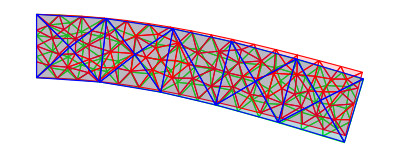

```mathematica
{lu, lv} = solve[1,  0.05]; {qu, qv} = solve[2, .05]; {qcu, qcv} = solve[2, 0.5];
Show[{plotSolution[qu, qv, Green, Opacity[0.15, Green]],plotSolution[lu, lv, Red, Opacity[0.15, Red]], plotSolution[qcu, qcv, Blue, Opacity[.15, Blue]]}, ImageSize->Full]
```

```mathematica
NumberForm[{qcu[1.37,0.37],qcv[1.37,0.37]},20]
```

{-0.01806653405994645,-0.1071282914512986}

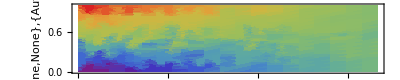

```mathematica
Show[mstrainPlot[lu, lv, 2, 20], ImageSize->Full]
```

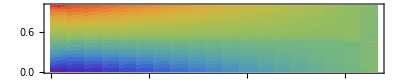

```mathematica
Show[mstrainPlot[qu,qv, 2, 20], ImageSize->Full]
```

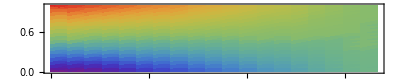

```mathematica
Show[mstrainPlot[qcu,qcv, 2, 20], ImageSize->Full]
```

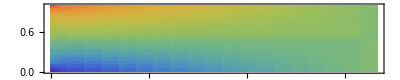

```mathematica
Show[mstrainPlot[quadU,quadV, 2, 20], ImageSize->Full]
```